```mathematica
(* define constants *)

size=61;
allNeighbors=9;
radius = 0.23;
width = 0.85;
tolerance = 0.4;
numNeighbor=41;
posNoise = 0.0775;
```

```mathematica
(* define lattice geometry *)
Hexagon[x0_,y0_,w_]=Polygon[Table[{x0,y0}+w/(√3){Cos[corner 60°-90°],Sin[corner 60°-90°]},{corner,0,5}]];
Offsets=Flatten[Table[row{1,0}+col{Cos[120°],Sin[120°]},{col,0,8,1},{row,0+Max[0,col-4],4+col-Max[0,col-4],1}],1];
Lattice=Show[Graphics[MapIndexed[{White,EdgeForm[Directive[Black,Thickness[0.0015]]],Hexagon[#[[1]],#[[2]],width],Black}&,
Offsets]]];
nf=Nearest[Offsets->Automatic,DistanceFunction->EuclideanDistance];

(*define position maps *)

Positions=MapIndexed[{Subscript[x, #2[[1]]][t],Subscript[y, #2[[1]]][t]}&,Offsets];
PositionValues:=posNoise*{RandomReal[{-1,1}],RandomReal[{-1,1}]}&/@Offsets;
PositionMap[values_]:=#[[1]]->#[[2]]&/@Transpose[{Flatten[Positions],Flatten[values]}];

(* define hexagonal potential well *)

CellPotential[x_,y_,R_]=-R/(1+Exp[(0.48-R-#)/0.015])&@(√(x^2+y^2)/(5389/5184-2/45 Cos[6ϕ]+1/180 Cos[12ϕ]-2/2835 Cos[18ϕ]+1/20160 Cos[24ϕ])/.ϕ->ArcTan[x,y]);

(* neighbor interactions *)

state = Transpose[{Offsets,Table[ radius,{i,1,61,1}]}];

neighbors=MapIndexed[Complement[nf[#1,{size,numNeighbor}],#2]&,Offsets];
potential[id_,R_]:=Plus@@(2/π ArcSin[R/(√((#[[1]])^2+(#[[2]])^2))]&@(#-Offsets[[id]]-{xx,yy})&/@(Offsets[[neighbors[[id]]]]+Positions[[neighbors[[id]]]]));

cpot=Compile[Evaluate[{#,_Real}&/@Flatten[Positions]],
Evaluate[Total[MapIndexed[(potential[#2[[1]],#1[[2]]]/.{xx->Subscript[x, #2[[1]]][t],yy->Subscript[y, #2[[1]]][t]})&,state]]]]

force[id_,R_]:=({D[#, xx],D[#, yy]}&@(potential[id,R]+CellPotential[xx,yy,R]))/.{xx->Subscript[x, id][t],yy->Subscript[y, id][t]};

equations=Flatten[MapIndexed[Equal@@#&/@Transpose[{{Subscript[x, #2[[1]]]'[t],Subscript[y, #2[[1]]]'[t]},force[#2[[1]],radius]}]&,Offsets],1];

(* solve equations of motion *)

DoSolve[InitialPositions_]:=Block[{InitialConditions=Equal@@#&/@Transpose[{Flatten[Positions/.t->0],
Flatten[InitialPositions]}]},NDSolve[Join[equations,InitialConditions,
{WhenEvent[Evaluate[Or@@(#≠0&/@Im[Flatten[Positions]])],"StopIntegration"],WhenEvent[Evaluate[And@@((N[-10^-8]<#<N[10^-8])&/@Flatten[D[Positions, t]])],"StopIntegration"]}],
Positions,
{t,0,1000},
Compiled->True,
StepMonitor:>(mon=MonitorPlot[Positions])]];


MonitorPlot[pos_]:=Show[{Lattice,Graphics[{Thickness[0.0015],Circle[#[[1]],#[[2]]]&/@Transpose[{(pos+state[[All,1]]), state[[All,2]]}]}]}]
```

Null^15 CompiledFunction[{Subscript$15818, Subscript$15819, Subscript$15820, Subscript$15821, Subscript$15822, Subscript$15823, Subscript$15824, Subscript$15825, Subscript$15826, Subscript$15827, Subscript$15828, Subscript$15829, Subscript$15830, <<102>>, Subscript$15933, Subscript$15934, Subscript$15935, Subscript$15936, Subscript$15937, Subscript$15938, Subscript$15939}, <<1>>, <<13>>-]

```mathematica
Monitor[tsol=DoSolve[PositionValues],mon];
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 55.3131 and t = 58.4683.

```mathematica
(* identify vertex structures *)

NearestNeighbors = MapIndexed[Complement[nf[#1,{7,1.1}],#2]&,Offsets];

PossibleTriplets=Block[{id,tmp},
DeleteDuplicates[Flatten[MapIndexed[DeleteDuplicates[Flatten[(id=#2[[1]];(tmp=#[[1]];{id,tmp,#}&/@Intersection[NearestNeighbors[[id]],#[[2]]])&/@Transpose[{#1,NearestNeighbors[[#1]]}]),1],SubsetQ]&,NearestNeighbors],1],SubsetQ]];
GetTriplets[PosValues_]:=Block[{dualoff},
Select[{#[[1]],dualoff=#[[2]];Max[Norm[(PosValues[[#]]+Offsets[[#]]-dualoff)]&/@#[[1]]]}&/@DualOffsets,#[[2]]<tolerance&][[All,1]]
]

DualOffsets={#,Mean[Offsets[[#]]]}&/@PossibleTriplets;
GetDualCounts[PosValues_]:=Block[{dualoff},
{dualoff=#[[2]],Length[Select[Norm[(PosValues[[#]]+Offsets[[#]]-dualoff)]&/@#[[1]],#<tolerance&]]}&/@DualOffsets
];

Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]
GetTMax[solution_]:=InterpolatingFunctionDomain[Head[solution[[1,1,2,1]]]][[1,2]];
GetAllPositions[solution_,time_]:=solution[[1,All,2]]/.t->time;
GetFinalPositions[solution_]:=Block[{tmax=GetTMax[solution]},(solution[[1,All,2]]/.t->tmax)];
GetEnergy[solution_]:=Total[Which[#==0,0,#==3,1,#==2,2,#==1,3]&/@GetDualCounts[GetFinalPositions[solution]][[All,2]]];

(* visualize results *)

PlotTriplets[solution_]:=(
Block[{},
Show[
Lattice,
Graphics[{LightGray,Hexagon[#[[1]],#[[2]],width]&/@Offsets[[#]]&/@GetTriplets[solution]}],
Graphics[{Thickness[0.0015],Circle[#[[1]],#[[2]]]&/@Transpose[{(solution+state[[All,1]]), state[[All,2]]}]}]
 ]
]
)

Trajectories[solution_] :=Block[{tmax=GetTMax[tsol]},Show[Join[{Lattice,Graphics[{Thickness[0.0015],Circle[#[[1]], #[[2]]]&/@Transpose[{(GetFinalPositions[tsol]+state[[All,1]]), state[[All,2]]}]}]},ParametricPlot[#,{t,0,tmax},PlotStyle->Directive[Red,JoinForm["Round"],CapForm["Round"],Thickness[0.006]]]&/@(GetAllPositions[solution,t]+state[[All,1]])],PlotRange->All]]

dualLattice[solution_] := Block[{tmax=GetTMax[solution]},Show[{Graphics[{White,EdgeForm[Directive[LightGray,Thickness[0.0015]]],Hexagon[#[[1]],#[[2]],width]&/@Offsets}],Graphics[{Thickness[0.003],LightGray,Circle[#[[1]],#[[2]]]&/@Transpose[{(GetFinalPositions[tsol]+state[[All,1]]), state[[All,2]]}]}],Graphics[{Opacity[0],EdgeForm[Directive[Gray,Thickness[0.0015]]],Polygon[Offsets[[#]]]&/@PossibleTriplets}],Graphics[{Which[#[[2]]==1,Black,#[[2]]==2,Blue,#[[2]]==3,Red,True,Gray],Text[#[[2]],#[[1]],{0,0}]}&/@GetDualCounts[GetFinalPositions[solution]]]}]]
```

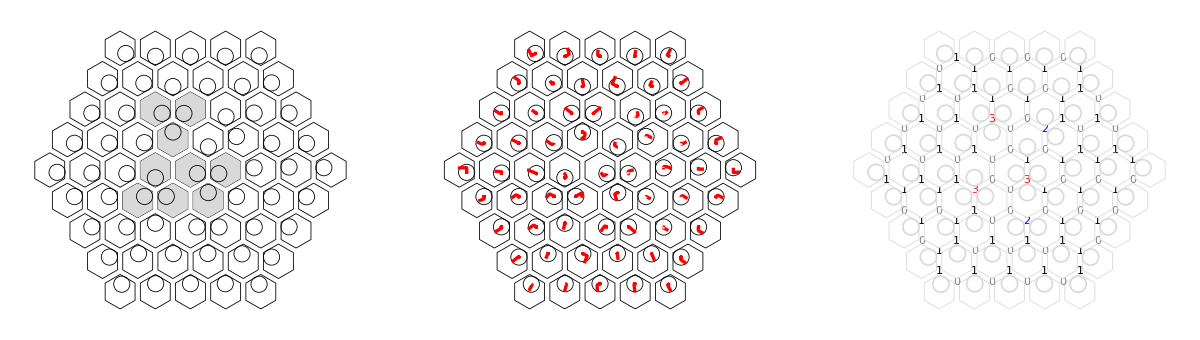

```mathematica
visualPanel = Show[GraphicsGrid[{{PlotTriplets[GetFinalPositions[tsol]], Trajectories[tsol], dualLattice[tsol]}},ImageSize->1200]]
```